```mathematica
a = 3
b = 5
c =2
d=4
```

3

5

2

4

```mathematica
a
```

3

```mathematica
FullForm[a b + c d]
```

23

```mathematica
TreeForm[a b + c d]
```

-Graphics-

```mathematica
Clear[{a,b,c,d}]
```

Clear::ssym: {a,b,c,d} is not a symbol or a string.

```mathematica
ClearAll[a,b,c,d]
```

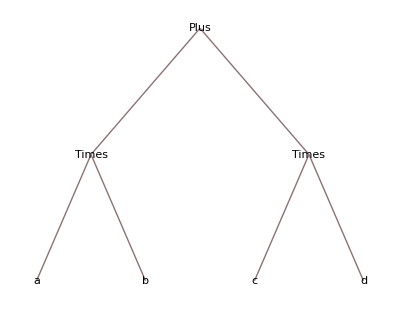

```mathematica
TreeForm[a b + c d]
```

```mathematica
TraditionalForm[a b +c d]
```

a b+c d

```mathematica
x = 10
2^x
```

10

1024

```mathematica
x ==5
```

False

```mathematica
Clear[a]
```

```mathematica
a  = 10 + 20-18
2^a+3^a+4^a
```

12

17312753

```mathematica
a = 10 + 20 - 18; 2^a+3^a+4^a
```

17312753

```mathematica
{i, 1, 10}
```

{i,1,10}

```mathematica
Table[i^2,{i, 1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i, 1,10,2}]
```

{1,9,25,49,81}

```mathematica
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[π,10]
```

{π,π,π,π,π,π,π,π,π,π}

```mathematica
Table[{i,i^2},{i,1,10,1}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
π squared is N[π^2]
```

31.0063 is squared

```mathematica
StringJoin["The first part ","and the second part."]
```

The first part and the second part.

```mathematica
ToString[N[π^2]]
```

9.8696

```mathematica
FullForm[%]
```

"9.8696"

```mathematica
StringJoin["π squared is:",ToString[N[π^2]]]
```

π squared is:9.8696

WolframAlphaQueryParseResults

2 ft

```mathematica
LinguisticAssistant+LinguisticAssistant
```

1504/127 ft

```mathematica
Quantity[3, "Meters"]
```

3 m

```mathematica
Quantity[2, "Meters"]+Quantity[3, "Feet"]
```

3643/381 ft

```mathematica
N[UnitConvert[Quantity[2, "Meters"]+Quantity[3, "Feet"],"Meters"],4]
```

2.914 m

```mathematica
QuantityMagnitude[Quantity[2.9144`4.,"Meters"]]
```

2.914

```mathematica
UnitConvert[%, "Centimeters"]
```

Quantity::compat: DimensionlessUnit and Centimeters are incompatible units

$Failed

```mathematica
Quantity[2,"Feet"]+Quantity[3, "Meters"]
```

1504/127 ft

```mathematica
UnitConvert[%, "Meters"]
```

2256/625 m

```mathematica
UnitConvert[Quantity[2256/625,"Meters"],"PlanckLength"]
```

2.233×10^35 l_P

```mathematica
Quantity[7,"Days"]+Quantity[2, "Weeks"]
```

21 days

```mathematica
Today
```

Sun 22 Aug 2021

```mathematica
DateList[DateObject[Today]]
```

{2021,8,22,0,0,0.}

```mathematica
DatePlus[DateObject[{2011,12,09},10^4]]
```

DateObject::notgran: 10000 is not a valid granularity specification for calendar Automatic.

DatePlus::inc: DateObject[{2011,12,9},10000] is not a recognized calendar increment specification for DatePlus.

```mathematica
DatePlus[DateObject[{2011,12,9},10000]]
```

DateObject::notgran: 10000 is not a valid granularity specification for calendar Automatic.

DatePlus::inc: DateObject[{2011,12,9},10000] is not a recognized calendar increment specification for DatePlus.

```mathematica
DatePlus[DateObject[{2011,12,9},10]]
```

DateObject::notgran: 10 is not a valid granularity specification for calendar Automatic.

DatePlus::inc: DateObject[{2011,12,9},10] is not a recognized calendar increment specification for DatePlus.

```mathematica
DatePlus[DateObject[{1983,02,04}],1.4*10^4]
```

Fri 4 Jun 2021

```mathematica
DayName[DateObject[{2017,07,29}]]
```

Saturday

```mathematica
DatePlus[Today,Quantity[4,"Weeks"]]
```

Sun 19 Sep 2021

```mathematica
DayName[DatePlus[Today,Quantity[4,"Weeks"]]]
```

```mathematica
Sunday

f[x_]:=x^2
```

Sunday

```mathematica
f[2]
```

4

```mathematica
f[π]
```

π^2

```mathematica
f[{1,2,3}]
```

{1,4,9}

```mathematica
h[a_,b_]:= a^b
```

```mathematica
h[2,3]
```

8

```mathematica
h[10,10,10]
```

h[10,10,10]

```mathematica
t = 7
```

7

```mathematica
3 t^2+2t+1
```

162

```mathematica
v = 6.5;
w = 7.1;
w^2-v^2
```

8.16

```mathematica
f[z_] := Sin[z];
myResponse = f[3];
N[myResponse,5]
```

0.14112

```mathematica
Table[f[i],{i,10}];
N[%,2]
```

{0.84,0.91,0.14,-0.76,-0.96,-0.28,0.66,0.99,0.41,-0.54}

```mathematica
Quantity[20, "Ounces"]
UnitConvert[%,"Kilograms"]
```

20 oz

45359237/80000000 kg

```mathematica
UnitConvert[Quantity[600, "Kilograms"],"Pounds"]
```

60000000000/45359237 lb

```mathematica
QuantityForm[Quantity[60000000000/45359237,"Pounds"],"Abbreviation"]
```

60000000000/45359237 lb

```mathematica
QuantityMagnitude[Quantity[60000000000/45359237,"Pounds"]]
```

60000000000/45359237